# Graviton Basis Toolkit Validation Report

This notebook is the notebook and PDF rendering of graviton_basis_toolkit_validation_report.md. It documents the validation strategy and records the current test outcome.

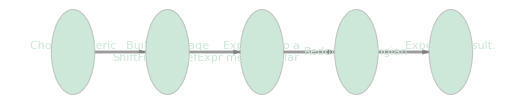

## Validation Strategy

The reducer is tested on expressions that are guaranteed to be redundant: images of the Fierz-Pauli kinetic term under nonlinear field redefinitions. In EFT language these are EOM-proportional terms up to a total derivative.

Choose a generic rank-2 redefinition from the computed RedefDeltaBasis.

Map it into the target scalar sector with ShiftFromRedefExpr.

Expand the result into a large scalar expression.

Reduce the expression with ReduceLagrangian.

Require the reduced representative to vanish exactly.

## Current Results

The table below comes from graviton_basis_toolkit_validation_output.wl.

Sector | IBPCount | RedefRank | PhysicalCount | DeltaBasisLength | LagTermCount | Reduced to 0?
{3,2} | 14 | 4 | 10 | 4 | 18 | True
{3,4} | 64 | 33 | 31 | 33 | 240 | True

### Interpretation

The {3,2} test is a compact sanity check. The {3,4} test is the stronger one because it uses all 33 rank-2 redefinition basis elements in that sector and expands to 240 scalar terms before reduction.

## Re-run Command

```mathematica
& 'C:\Program Files\Wolfram Research\Wolfram\14.2\WolframKernel.exe' -script graviton_basis_toolkit_validation.wls
```

After rerunning, inspect graviton_basis_toolkit_validation_output.wl for the updated association.

## Files Produced by the Validation

graviton_basis_toolkit_validation.wls: validation script

graviton_basis_toolkit_validation_output.wl: machine-readable output

graviton_basis_validation_cache/: persistent cache used by the validation run